```mathematica
solutions=Import[StringJoin[NotebookDirectory[],"training_grid.dat"],"Table"];
Length[solutions]
finalSNRs=Flatten[Import[StringJoin[NotebookDirectory[],"sec14SNRs.dat"],"Table"]];
Length[finalSNRs]
```

103447

103447

```mathematica
"{p,b,P}";
prange={Min[solutions[[All,1]]],Max[solutions[[All,1]]]}
brange={Min[solutions[[All,2]]],Max[solutions[[All,2]]]}
Prange={Min[solutions[[All,3]]],Max[solutions[[All,3]]]}
```

{0.0699839,13.9968}

{0.01,13.0667}

{0.1,10.}

```mathematica
"define min/max R";
REarth=6378100;
Rmin=0.1 REarth;
Rmax=20 REarth;
"define Rstar";
RSun=6.957*10^8;
Rstar=0.0131RSun;
"define min/max P";
Pmin=0.1;Pmax=10;
"convert a p value to a grid position from 1 to n=54";
ptoip[p_]:=Round[((54-1)((Log[p Rstar]-Log[Rmin])/(Log[Rmax]-Log[Rmin]))+1)];
pmax=Max[solutions[[All,1]]];bmin=0.01;
"convert a p value to a grid position from 1 to n-1=53";
btoib[b_]:=Round[((Log[b]-Log[bmin])/((Log[1+pmax]-Log[bmin])/(54-1))+1)];
"convert a p value to a grid position from 1 to m=47";
PtoiP[P_]:=Round[((Log[P]-Log[Pmin])/((Log[Pmax]-Log[Pmin])/(47-1))+1)];
"continuous versions";
ptoip2[p_]:=((54-1)((Log[p Rstar]-Log[Rmin])/(Log[Rmax]-Log[Rmin]))+1);
btoib2[b_]:=((Log[b]-Log[bmin])/((Log[1+pmax]-Log[bmin])/(54-1))+1);
PtoiP2[P_]:=((Log[P]-Log[Pmin])/((Log[Pmax]-Log[Pmin])/(47-1))+1);
```

```mathematica
"define unique positions";
uniqueps=Union[solutions[[All,1]]];
uniquebs=Union[solutions[[All,2]]];
uniquePs=Union[solutions[[All,3]]];
```

```mathematica
Length[uniquePs]*Length[uniqueps]*Length[uniquebs]
```

134514

```mathematica
SNRgoal=10;
tolerance=10^-3;
```

```mathematica
origx=Table[{solutions[[i]],finalSNRs[[i]]},{i,1,Length[finalSNRs]}];
j=0;Label[jloop];j=j+1;"select only periods=P_j";thisrow=Select[origx,#[[1]][[3]]==uniquePs[[j]]&];"delete period info from this line";thisrow=Table[{thisrow[[i,1]][[{1,2}]],thisrow[[i,2]]},{i,1,Length[thisrow]}];"find IDs in p-b space";presentIDs=thisrow[[All,1]];presentsIDs=Table[{ptoip[presentIDs[[i,1]]],btoib[presentIDs[[i,2]]]},{i,1,Length[presentIDs]}];"identify missing IDs";missingIDs=Select[Flatten[Table[{i1,i2},{i1,1,Length[uniqueps]},{i2,1,Length[uniquebs]}],1],!MemberQ[presentsIDs,#]&];missingrow=Table[{{uniqueps[[missingIDs[[i,1]]]],uniquebs[[missingIDs[[i,2]]]]},0},{i,1,Length[missingIDs]}];"combine missing row with original";fullrow=Union[thisrow,missingrow];fullrowID=Table[{{ptoip[fullrow[[i,1]][[1]]],btoib[fullrow[[i,1]][[2]]]},fullrow[[i,2]]},{i,1,Length[fullrow]}];"perform the interpolation";interp=Interpolation[fullrowID,Method->"Hermite",InterpolationOrder->3];k=0;Label[kloop];k=k+1;minimize=NMinimize[{(interp[ptoip2[p],btoib2[uniquebs[[k]]]]-SNRgoal)^2,prange[[1]]≤p≤prange[[2]]},p,Method->"DifferentialEvolution"];If[First[minimize]>tolerance,minimize=NMinimize[{(interp[ptoip2[p],btoib2[uniquebs[[k]]]]-SNRgoal)^2,prange[[1]]≤p≤prange[[2]]},p,Method->"SimulatedAnnealing"]];Subscript[psol, k]=Last[Last[Last[minimize]]];Subscript[quality, k]=First[minimize];If[k<Length[uniquebs],Goto[kloop]];test=Table[{uniquebs[[k]],Subscript[psol, k],Subscript[quality, k]},{k,1,Length[uniquebs]}];good=Select[test,#[[3]]<tolerance&][[All,{1,2}]];bad=Select[test,#[[3]]>tolerance&][[All,{1,2}]];If[MemberQ[bad[[All,1]],First[uniquebs]]||MemberQ[bad[[All,1]],Last[uniquebs]],intergood=Interpolation[good,Method->"Hermite",InterpolationOrder->2],intergood=Interpolation[good,Method->"Hermite",InterpolationOrder->1]];If[Length[bad]>0,betterbad=Table[{bad[[i,1]],intergood[bad[[i,1]]]},{i,1,Length[bad]}],betterbad={}];If[Length[bad]>0,Subscript[contour, j]=Sort[Join[good,betterbad]],Subscript[contour, j]=test[[All,{1,2}]]];If[j<Length[uniquePs],Goto[jloop]];
```

InterpolatingFunction::dmval: Input value {24.1333,53.0015} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.63379,53.0015} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.12087,53.0015} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

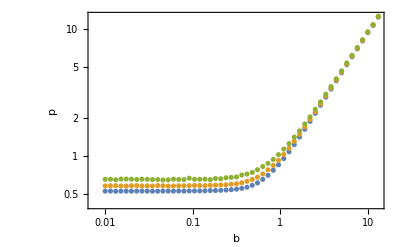

```mathematica
ListLogLogPlot[{Subscript[contour, 1],Subscript[contour, 10],Subscript[contour, 20]},PlotRange->All,Frame->True,FrameLabel->{"b","p"}]
```

Things get pretty compact between the contours, we want to ensure a smooth monotonic function in period space. So let’s plot it out for each b point and enforce a monotonic function...

```mathematica
B=0;Label[Bloop];B=B+1;bslice=Table[{iP,Subscript[contour, iP][[B]][[2]]},{iP,1,Length[uniquePs]}];lm=LinearModelFit[bslice,{iP,iP^2},iP,IncludeConstantBasis->True,Weights->bslice[[All,1]]^-1];Subscript[bslicebetter, B]=Table[{iP,lm[iP]},{iP,1,Length[uniquePs]}];If[B<Length[uniquebs],Goto[Bloop]];
```

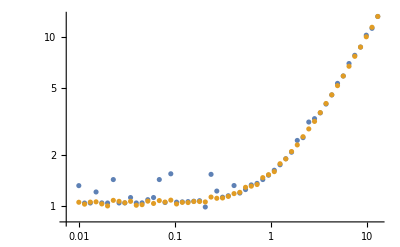

```mathematica
iP=0;Label[Ploop];iP=iP+1;Subscript[newcontour, iP]=Table[{Subscript[contour, iP][[B,1]],Subscript[bslicebetter, B][[iP]][[2]]},{B,1,Length[uniquebs]}];If[iP<Length[uniquePs],Goto[Ploop]];
ListLogLogPlot[{Subscript[contour, iP],Subscript[newcontour, iP]}]
```

```mathematica
iP=0;Label[Ploop];iP=iP+1;Subscript[finalcontour, iP]=Table[{Log10[uniquePs[[iP]]],Subscript[newcontour, iP][[i,1]],Subscript[newcontour, iP][[i,2]]},{i,1,Length[Subscript[newcontour, iP]]}];If[iP<Length[uniquePs],Goto[Ploop]];
```

```mathematica
contours=Flatten[Table[Subscript[finalcontour, iP],{iP,1,Length[uniquePs]}],1];
```

```mathematica
Export[StringJoin[NotebookDirectory[],"detection_contours.dat"],contours,"Table"]
```